```mathematica
(* The system is a unit square with a rod in the middle. 
We will do operator splitting on epsilon=0.02 and compare it to the non-split system and the without rod system. 
The diffusion constant of the sheet will be 0.02


To save computation time in display the cross-section at y=0.5 is shown*)
```

```mathematica
maxT2=10;  (*Time to calculate until*)
```

```mathematica
initF[x_,y_]:=20x(x-1)y(y-1); (*Initial temperature of sheet*)
```

```mathematica
initFvals = Table[vals2[i/100,0.5,ti*maxT2/100],{i,0,100},{ti,0,100}];
```

```mathematica
allFvals = {initFvals};  (*Table of temperature values*)
```

```mathematica
epsilon = 0.02;
```

```mathematica
curY = 0.5;
```

```mathematica
alphaRodValues = {0.05,0.1,0.2};
```

```mathematica
alphaSheet = 0.02;
```

```mathematica
(*Original System Before Operator Splitting*)
```

```mathematica
vals2 = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0||x==1||y==0||y==1],DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,maxT2}] (*Temperature of sheet if no rod*)
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

InterpolatingFunction[{{0., 1.}, {0., 1.}, {0., 10.}}, <>]

```mathematica
nonRodValues = Table[vals2[i/100,curY,maxT2*ti/100],{i,0,100},{ti,0,100}];
```

```mathematica
epsilonValues = {0.1,0.02,0.01};
```

```mathematica
allPreSplitValues = {nonRodValues};
```

```mathematica
Do[(alphaRod = alphaRodValues[[curInd]];vals3 = NDSolveValue[{D[u[x,y,t],t]-alphaRod*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0||x==1||y==0||y==1],DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,1},{y,0,1},{t,0,maxT2}];
vals3Deriv[x_,y_,t_]:=D[vals3[xx,yy,tt],tt]/.{xx->x,tt->t,yy->y};
vals2Left = NDSolveValue[{D[u[x,y,t],t]-0.02*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0||y==0||y==1]+NeumannValue[vals3Deriv[x,y,t],x==0.5-epsilon],DirichletCondition[u[x,y,t]==vals3[x,y,t],x==0.5-epsilon],DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0,0.5-epsilon},{y,0,1},{t,0,maxT2}];
vals2Right = NDSolveValue[{D[u[x,y,t],t]-0.02*Laplacian[u[x,y,t],{x,y}]==NeumannValue[vals3Deriv[x,y,t],x==0.5+epsilon]+NeumannValue[0,x==1||y==0||y==1],DirichletCondition[u[x,y,t]==vals3[x,y,t],x==0.5+epsilon],DirichletCondition[u[x,y,t]==initF[x,y],t==0]},u,{x,0.5+epsilon,1},{y,0,1},{t,0,maxT2}];
wholePlotNoSplit[x_,y_,t_]:=Piecewise[{{vals2Left[x,y,t],x≤ 0.5-epsilon},{vals3[x,y,t],x>0.5-epsilon && x ≤ 0.5+epsilon},{vals2Right[x,y,t],x>0.5+epsilon}}];
nonSplitValues = Table[wholePlotNoSplit[i/100,curY,maxT2*ti/100],{i,0,100},{ti,0,100}]; AppendTo[allPreSplitValues,nonSplitValues]),{curInd,1,Length[alphaRodValues]}];
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

General::stop: Further output of NDSolveValue::femcscd will be suppressed during this calculation.

```mathematica
(*Here I will attempt the operator split system*)
```

```mathematica
NN=100; tau = maxT2/NN;
```

```mathematica
timeInd=1;
```

```mathematica
tempEndT = 5;
```

```mathematica
currentF [x_,y_]:=initF[x,y];
```

```mathematica
initialValues = Table[initF[i/100,curY],{i,0,100}];
```

```mathematica
foobar = Table[i,{i,0,3}]
```

{0,1,2,3}

```mathematica
foobar2 = Table[i+10,{i,0,3}]
```

{10,11,12,13}

```mathematica
initFoo = {{foobar},{foobar},{foobar}}
```

{{{0,1,2,3}},{{0,1,2,3}},{{0,1,2,3}}}

```mathematica
AppendTo[initFoo[[1]],foobar2]
```

{{0,1,2,3},{10,11,12,13}}

```mathematica
initFoo
```

{{{0,1,2,3},{10,11,12,13}},{{0,1,2,3}},{{0,1,2,3}}}

```mathematica
initFoo[[1,2]]
```

{10,11,12,13}

```mathematica
allValues = {{initialValues},{initialValues},{initialValues}};
```

```mathematica
Do[(alphaRod = alphaRodValues[[curInd]];Do[((*Iterate the rod for one time step. Doing O_{1D}. Neumann B.C. will be zero*)
rodVals = NDSolveValue[{D[u[x,y,t],t]-alphaRod*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0.5-epsilon||x==0.5+epsilon||y==0||y==1],DirichletCondition[u[x,y,t]==currentF[x,y],t==(timeInd-1)*tau]},u,{x,0.5-epsilon,0.5+epsilon},{y,0,1},{t,(timeInd-1)*tau,timeInd*tau}];
rodValsDeriv[x_,y_,t_]:=D[rodVals[xx,yy,tt],tt]/.{xx->x,tt->t,yy->y};
(*Iterate the left sheet for one time step. Doing O_{1->2}. Will match neumann values of rod and sheet to denote the energy transfer*)
sheetLeftValsWithRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0||y==0||y==1]+NeumannValue[rodValsDeriv[x,y,t],x==0.5-epsilon],DirichletCondition[u[x,y,t]==rodVals[x,y,t],x==0.5-epsilon],DirichletCondition[u[x,y,t]==currentF[x,y],t==(timeInd-1)*tau]},u,{x,0,0.5-epsilon},{y,0,1},{t,(timeInd-1)*tau,timeInd*tau}];
(*Iterate the right sheet for one time step. Doing O_{1->2}. Will match neumann values of rod and sheet to denote the energy transfer*)
sheetRightValsWithRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==NeumannValue[rodValsDeriv[x,y,t],x==0.5+epsilon]+NeumannValue[0,x==1||y==0||y==1],DirichletCondition[u[x,y,t]==rodVals[x,y,t],x==0.5+epsilon],DirichletCondition[u[x,y,t]==currentF[x,y],t==(timeInd-1)*tau]},u,{x,0.5+epsilon,1},{y,0,1},{t,(timeInd-1)*tau,timeInd*tau}];

(*Starting time step was rod then influencing the sheet. Next time step is sheet and then it influences the rod*)
curT = timeInd*tau;
currentF[x_,y_]:=Piecewise[{{sheetLeftValsWithRod[x,y,curT],x<0.5-epsilon},{rodVals[x,y,curT],x≥ 0.5-epsilon && x ≤ 0.5+epsilon},{sheetRightValsWithRod[x,y,curT],x>0.5+epsilon}}];

(*Iterate the left sheet assuming no rod influence. Doing O_{2D}. Make neumann b.c. equal to zero for this. *)
sheetLeftValsNoRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0||x==0.5-epsilon||y==0||y==1],DirichletCondition[u[x,y,t]==currentF[x,y],t==timeInd*tau]},u,{x,0,0.5-epsilon},{y,0,1},{t,timeInd*tau,(timeInd+1)*tau}];
sheetLeftDeriv[x_,y_,t_]:=D[sheetLeftValsNoRod[xx,yy,tt],tt]/.{xx->x,tt->t,yy->y};
(*Iterate the right sheet assuming no rod influence. Doing O_{2D}. Make neumann b.c. equal to zero for this *)
sheetRightValsNoRod = NDSolveValue[{D[u[x,y,t],t]-alphaSheet*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,x==0.5+epsilon||x==1||y==0||y==1],DirichletCondition[u[x,y,t]==currentF[x,y],t==timeInd*tau]},u,{x,0.5+epsilon,1},{y,0,1},{t,timeInd*tau,(timeInd+1)*tau}];
sheetRightDeriv[x_,y_,t_]:=D[sheetRightValsNoRod[xx,yy,tt],tt]/.{xx->x,tt->t,yy->y};
(*Iterate the rod assuming sheet influence. Doing O_{2->1}. Make neumann b.c. equals for this to happen*)
rodValsWithSheet = NDSolveValue[{D[u[x,y,t],t]-alphaRod*Laplacian[u[x,y,t],{x,y}]==NeumannValue[0,y==0||y==1]+NeumannValue[sheetLeftDeriv[x,y,t],x==0.5-epsilon]+NeumannValue[sheetRightDeriv[x,y,t],x==0.5+epsilon],DirichletCondition[u[x,y,t]==sheetLeftValsNoRod[x,y,t],x==0.5-epsilon],DirichletCondition[u[x,y,t]==sheetRightValsNoRod[x,y,t],x==0.5+epsilon],DirichletCondition[u[x,y,t]==currentF[x,y],t==timeInd*tau]},u,{x,0.5-epsilon,0.5+epsilon},{y,0,1},{t,timeInd*tau,(timeInd+1)*tau}];

curT = (timeInd+1)*tau;
currentF[x_,y_]:=Piecewise[{{sheetLeftValsNoRod[x,y,curT],x<0.5-epsilon},{rodValsWithSheet[x,y,curT],x≥ 0.5-epsilon && x ≤ 0.5+epsilon},{sheetRightValsNoRod[x,y,curT],x>0.5+epsilon}}];

currentValues = Table[currentF[i/100,curY],{i,0,100}];
AppendTo[allValues[[curInd]],currentValues];),{timeInd,1,tempEndT}];),{curInd,1,3}]
(*wholePlotNoSplit[x_,y_,t_]:=Piecewise[{{vals2Left[x,y,t],x≤ 0.5-epsilon},{vals3[x,y,t],x>0.5-epsilon && x ≤ 0.5+epsilon},{vals2Right[x,y,t],x>0.5+epsilon}}];*)
```

NDSolveValue::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

General::stop: Further output of NDSolveValue::femcscd will be suppressed during this calculation.

```mathematica
(*Plot the results*)
```

```mathematica
Manipulate[ListPlot[{allValues[[1,t]],allValues[[2,t]],allValues[[3,t]],allPreSplitValues[[1]][[All,t]],allPreSplitValues[[2]][[All,t]],allPreSplitValues[[3]][[All,t]],allPreSplitValues[[4]][[All,t]],Table[1.2,{i,100}]},Joined->True,PlotLegends->{"Operator Split System Results, AlphaRod=0.05","Operator Split System Results, AlphaRod=0.1","Operator Split System Results, AlphaRod=0.2","Sheet without the Rod","Results Before Operator Splitting, AlphaRod=0.05","Results Before Operator Splitting, AlphaRod=0.1","Results Before Operator Splitting, AlphaRod=0.2","Constant"}],{t,1,tempEndT,1}]
```

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partd: Part specification allValues⟦80⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

```mathematica
(*Shows the First Step and Plot Legend*)
```

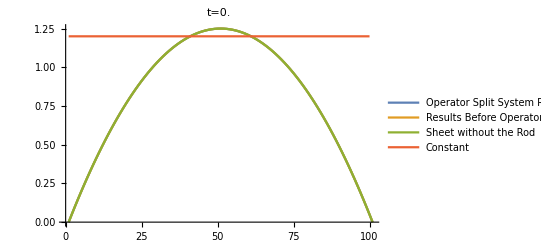

```mathematica
(* (t=1;dispT = (t-1)/100 //N;ListPlot[{allValues[[t]],nonSplitValues[[All,t]],nonRodValues[[All,t]],Table[1.2,{i,100}]},Joined->True,PlotLegends->{"Operator Split System Results","Results Before Operator Splitting","Sheet without the Rod","Constant"},PlotLabel->StringJoin["t=",ToString[dispT]]]) *)
```

```mathematica
(*Shows Subsequent Time Steps*)
```

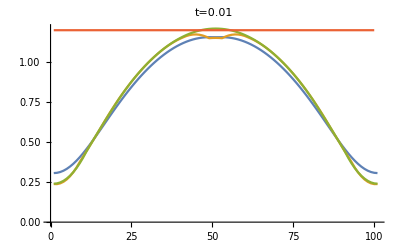
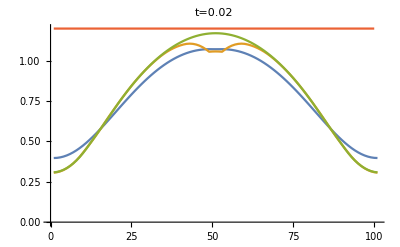
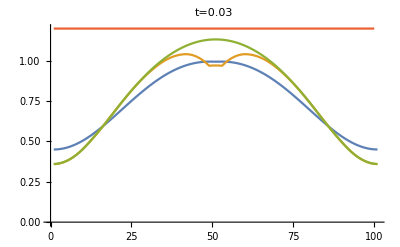
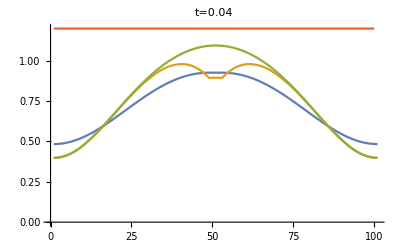
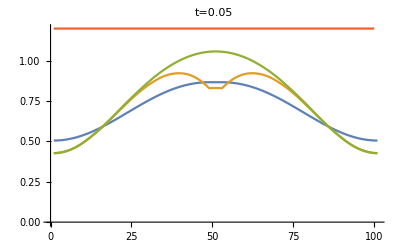
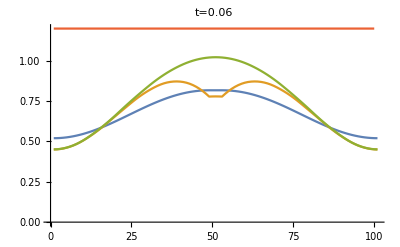
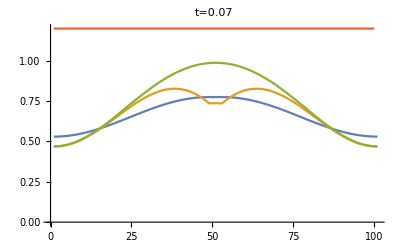
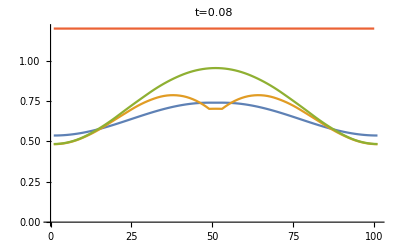

```mathematica
(* Table[(dispT = (t-1)/100 //N;ListPlot[{allValues[[t]],nonSplitValues[[All,t]],nonRodValues[[All,t]],Table[1.2,{i,100}]},Joined->True,PlotLabel->StringJoin["t=",ToString[dispT]]]),{t,2,tempEndT,1}] *)
```